### Computation of the Entanglement Entropy: Generalized Bell States

```mathematica
Ψ={{-Graphics-, "QuantumState"}}[<|{0,1}->Cos[θ],{1,0}->-Sin[θ]|>,2,2]
```

QuantumState[…]

```mathematica
Ψ["DensityMatrix"]//MatrixForm
```

(0 | 0 | 0 | 0
0 | Conjugate[Cos[θ]] Cos[θ] | -Conjugate[Sin[θ]] Cos[θ] | 0
0 | -Conjugate[Cos[θ]] Sin[θ] | Conjugate[Sin[θ]] Sin[θ] | 0
0 | 0 | 0 | 0)

```mathematica
Ψ["Formula"]
```

Cos[θ] 01-10 Sin[θ]

```mathematica
𝓇=Simplify[QuantumPartialTrace[Ψ,{2}]["DensityMatrix"]]
```

SparseArray[…]

Compute the Entanglement Entropy: S_𝓇

```mathematica
S=Simplify[-Tr[𝓇.MatrixLog[𝓇]],Assumptions->0<=θ<=π/2]
```

-2 (Cos[θ]^2 Log[Cos[θ]]+Log[Sin[θ]] Sin[θ]^2)

Find the maximum entanglement value

```mathematica
S//.Solve[D[S,θ]==0,θ][[1]]
```

Log[2]

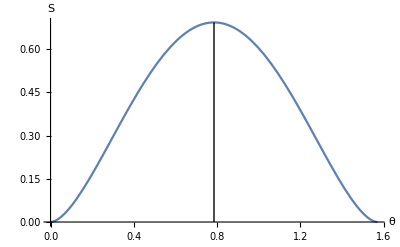

```mathematica
Plot[{S},{θ,0,π/2},AxesLabel->{θ,HoldForm[S]},Epilog->Line[{{π/4,Simplify[S//.{θ->π/4}]},{π/4,0}}]]
```